## CIP0 derivation;

```mathematica
ClearAll["Global`*"]
```

```mathematica
F[x_]:=a+b(x-ξ)+c(x-ξ)^2+d(x-ξ)^3
```

```mathematica
Constrains;
```

```mathematica
Right-Bias;
RBiasEqn={
F[ξ]==Subscript[f, i],
F[ξ+h]==Subscript[f, i+1],
(D[F[x],x]/.x->ξ)==Subscript[g, i],
(D[F[x],x]/.x->ξ+h)==Subscript[g, i+1]
};
RBiasEqnSol=Solve[RBiasEqn,{a,b,c,d}];
Style[Row[{
Column[RBiasEqnSol//Flatten,Spacings->2],
},Spacer[8]],FontSize->16]//ExpandAll//TraditionalForm
```

a→f_i
b→g_i
c→-(3 f_i)/h^2+(3 f_(i+1))/h^2-(2 g_i)/h-(g_(i+1))/h
d→(2 f_i)/h^3-(2 f_(i+1))/h^3+g_i/h^2+(g_(i+1))/h^2

#### Hermite spline basis funstion; https://en.wikipedia.org/wiki/Cubic_Hermite_spline; https://www.siggraph.org/education/materials/HyperGraph/modeling/splines/hermite.htm;

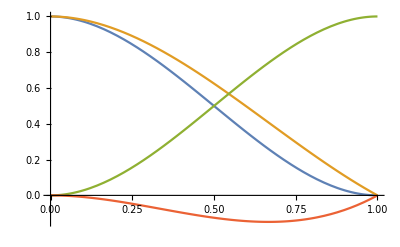

```mathematica
h0[x_]:=2(x-ξ)^3-3(x-ξ)^2+1
h1[x_]:=(x-ξ)^3-2(x-ξ)^2+1
h2[x_]:=-2(x-ξ)^3+3(x-ξ)^2
h3[x_]:=(x-ξ)^3-(x-ξ)^2
Plot[{h0[x]/.ξ->0,h1[x]/.ξ->0,h2[x]/.ξ->0,h3[x]/.ξ->0},{x,0,1}]
```

```mathematica
Clear[a,b,c,d]
```

```mathematica
F0[x_]:=a h0[x]+b h1[x]+c h2[x]+d h3[x]
```

```mathematica
Right-Bias;
RBiasEqn={
F0[ξ]==Subscript[f, i],
F0[ξ+h]==Subscript[f, i+1],
(D[F0[x],x]/.x->ξ)==Subscript[g, i],
(D[F0[x],x,x]/.x->ξ+h)==Subscript[g, i+1]
};
RBiasEqnSol=Solve[RBiasEqn,{a,b,c,d}];
Style[Row[{
Column[RBiasEqnSol//Flatten,Spacings->2],
},Spacer[8]],FontSize->16]//ExpandAll//TraditionalForm
```

```mathematica
F0[ξ+h]
```

c (3 h^2-2 h^3)+b (1-2 h^2+h^3)+d (-h^2+h^3)+a (1-3 h^2+2 h^3)

```mathematica
D[F0[x],x]/.x->ξ
```

0

```mathematica
RBiasEqn
```

{a+b==f_i,c (3 h^2-2 h^3)+b (1-2 h^2+h^3)+d (-h^2+h^3)+a (1-3 h^2+2 h^3)==f_(1+i),0==g_i,c (6-12 h)+b (-4+6 h)+d (-2+6 h)+a (-6+12 h)==g_(1+i)}

```mathematica
D[F0[x],x,x]/.x->ξ+h//Simplify
```

-2 (-3 c+d+a (3-6 h)+b (2-3 h)+6 c h-3 d h)

```mathematica
Solve[RBiasEqn,{a,b,c,d}]
```

{}

#### B-spline cubic basis funstion;

## CIP5 derivation;

```mathematica
ClearAll["Global`*"]
```

### Reference : Masaki Tanigawa, Basic study on acoustic wave analysis by the multi-moment method using interpolation by a high-order polynomial, Proceedings of 20th International Congress on Acoustics, ICA 2010, 23–27 August 2010, Sydney, Australia

```mathematica
F2[x_]:=a1+a2(x-ξ)+a3(x-ξ)^2+a4(x-ξ)^3+a5(x-ξ)^4+a6(x-ξ)^5
```

```mathematica
Right-Bias;
RBiasEqn={
F2[ξ]==Subscript[f, i],
F2[ξ+dx]==Subscript[f, i+1],
(D[F2[x],x]/.x->ξ)==Subscript[g, i],
(D[F2[x],x]/.x->ξ+dx)==Subscript[g, i+1],
(D[F2[x],x,x]/.x->ξ)==Subscript[h, i],
(D[F2[x],x,x]/.x->ξ+dx)==Subscript[h, i+1]
};
RBiasEqnSol=Solve[RBiasEqn,{a1,a2,a3,a4,a5,a6}];
Style[Row[{
Column[RBiasEqnSol//Flatten,Spacings->2]
},Spacer[8]],FontSize->16]//ExpandAll//TraditionalForm
```

a1→f_i
a2→g_i
a3→h_i/2
a4→-(10 f_i)/dx^3+(10 f_(i+1))/dx^3-(6 g_i)/dx^2-(4 g_(i+1))/dx^2-(3 h_i)/(2 dx)+(h_(i+1))/(2 dx)
a5→(15 f_i)/dx^4-(15 f_(i+1))/dx^4+(8 g_i)/dx^3+(7 g_(i+1))/dx^3+(3 h_i)/(2 dx^2)-(h_(i+1))/dx^2
a6→-(6 f_i)/dx^5+(6 f_(i+1))/dx^5-(3 g_i)/dx^4-(3 g_(i+1))/dx^4-h_i/(2 dx^3)+(h_(i+1))/(2 dx^3)

## RCIP derivation;

### Reference :

```mathematica
ClearAll["Global`*"]
```

```mathematica
F3[x_]:=(a0+a1(x-ξ)+a2(x-ξ)^2)/(1+ b(x-ξ))
```

```mathematica
Constrains;
RBiasEqn={
F3[ξ]==Subscript[f, i],
F3[ξ+h]==Subscript[f, i+1],
(D[F3[x],x]/.x->ξ)==Subscript[d, i],
(D[F3[x],x]/.x->ξ+h)==Subscript[d, i+1]
};
RBiasEqnSol=Solve[RBiasEqn,{a0,a1,a2,b}];
Style[Row[{
Column[RBiasEqnSol//Flatten,Spacings->2]
},Spacer[8]],FontSize->16]//FullSimplify//Factor
```

a0→f_i
a1→d_i-(2 f_i)/h+((-d_i+d_(1+i)) f_i)/(h d_(1+i)+f_i-f_(1+i))
a2→(-h^2 d_i d_(1+i)+(f_i-f_(1+i))^2)/(h^2 (h d_(1+i)+f_i-f_(1+i)))
b→-2/h+(-d_i+d_(1+i))/(h d_(1+i)+f_i-f_(1+i))

```mathematica
Flatten[RBiasEqnSol][[4]]
```

b→(-h d_i-h d_(1+i)-2 f_i+2 f_(1+i))/(h (h d_(1+i)+f_i-f_(1+i)))

```mathematica
ClearAll["Global`*"]
```

```mathematica
b=(-h Subscript[d, i]-h Subscript[d, 1+i]-2 Subscript[f, i]+2 Subscript[f, 1+i])/(h (h Subscript[d, 1+i]+Subscript[f, i]-Subscript[f, 1+i]))
```

(-h d_i-h d_(1+i)-2 f_i+2 f_(1+i))/(h (h d_(1+i)+f_i-f_(1+i)))

```mathematica
F4[x_]:=(a0+a1(x-ξ)+a2(x-ξ)^2+a3(x-ξ)^3)/(1+α b(x-ξ))
```

```mathematica
Constrains;
RBiasEqn={
F4[ξ]==Subscript[f, i],
F4[ξ+h]==Subscript[f, i+1],
(D[F4[x],x]/.x->ξ)==Subscript[d, i],
(D[F4[x],x]/.x->ξ+h)==Subscript[d, i+1]
};
RBiasEqnSol=Solve[RBiasEqn,{a0,a1,a2,a3}];
Style[Row[{
Column[RBiasEqnSol//Flatten,Spacings->2]
},Spacer[8]],FontSize->16]//FullSimplify//Factor
```

a0→f_i
a1→d_i-(2 α f_i)/h+(α (-d_i+d_(1+i)) f_i)/(h d_(1+i)+f_i-f_(1+i))
a2→(2 h (-1+α) d_i-h d_(1+i)+(-3+4 α) f_i)/h^2+(α d_(1+i) (-d_i+d_(1+i)))/(h d_(1+i)+f_i-f_(1+i))+((3-4 α) f_(1+i))/h^2
a3→-((-1+α) (h d_i+h d_(1+i)+2 f_i-2 f_(1+i)))/h^3

```mathematica
b
```

b